The supersymmetric transform method makes a transform of the potential to remove a forbidden state  by taking

 is the forbidden state wavefunction, which in the GEM is represented by 

Thus the second derivative of the log is


where  is the derivative of  with respect to r. These are represented by 


The supersymmetric potential is written as 

We now want to plot this using the forbidden  state in . Taking  with  and . We use the results of the python calculation to get the   for

```mathematica
hbar = 197
```

197

```mathematica
GenerateRangParams[numGaussians_Integer, r1_: 0.01, rmax_: 25] :=  Module[
{rn, a},
a = (r1/rmax)^(1/(1-numGaussians));
rn = Table[r1*a^i, {i, 0, numGaussians - 1}];
  rn
];
GenerateRangParams[20]
```

{0.01,0.0150952,0.0227865,0.0343967,0.0519225,0.0783781,0.118313,0.178596,0.269595,0.406959,0.614313,0.927317,1.3998,2.11303,3.18967,4.81487,7.26814,10.9714,16.5616,25.}

```mathematica
ForbiddenMixingCoeffs = List[1.27078932*10^-07,-6.28937678*10^-07,1.97121551*10^-06,-5.26305283*10^-06, 1.32208898*10^-05,-3.24517290*10^-05,7.90444426*10^-05,-1.92563784*10^-04, 4.72746598*10^-04,-1.18632051*10^-03, 3.15323043*10^-03,-9.84130038*10^-03,9.12681860*10^-02, 5.08136709*10^-01,3.65151534*10^-01, 1.04950742*10^-01, 2.95184421*10^-03, 1.32948720*10^-03,-6.77628354*10^-04,1.95095230*10^-04]
```

{1.27079×10^-7,-6.28938×10^-7,1.97122×10^-6,-5.26305×10^-6,0.0000132209,-0.0000324517,0.0000790444,-0.000192564,0.000472747,-0.00118632,0.00315323,-0.0098413,0.0912682,0.508137,0.365152,0.104951,0.00295184,0.00132949,-0.000677628,0.000195095}

```mathematica
GaussianRangeParams = GenerateRangParams[20];
GaussianWaveFuncNormalisation[αi_] := (2/(π αi^2))^(3/4)
GaussianWaveFunction[r_, c_, αi_]:=c* GaussianWaveFuncNormalisation[αi]*Exp[-r^2/αi^2]
ForbiddenWaveFunc[r_]= Sum[GaussianWaveFunction[r, ForbiddenMixingCoeffs[[i]], GaussianRangeParams[[i]]],{i, 20}];
DForbiddenWaveFunc[r_]=D[ForbiddenWaveFunc[r], r];
D2ForbiddenWaveFunc[r_]=D[DForbiddenWaveFunc[r], r];
CoreNeutronPotnetial[r_, V0_, β_]:=V0 Exp[-r^2/β^2]
```

```mathematica
SupersymmetricPotnetial[r_, V0_, β_, m_]:=CoreNeutronPotnetial[r,V0,β] -hbar^2/m (D2ForbiddenWaveFunc/ForbiddenWaveFunc-(DForbiddenWaveFunc/ForbiddenWaveFunc)^2)
```

```mathematica
PlotData=Table[{r,SupersymmetricPotnetial[r, -47.32,  2.30, 935*(4/5)]},{r, 0, 5, 0.1}];
ListPlot[PlotData,PlotRange-> All]
```

-Graphics-

```mathematica
Plot[SupersymmetricPotnetial[r, -47.32,  2.30, 935*(4/5)], {r,0,5}, PlotRange->Full]
```

-Graphics-

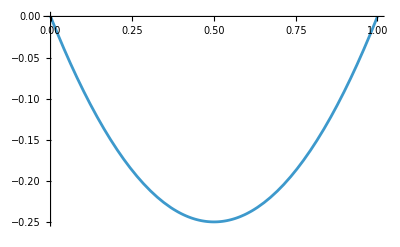

```mathematica
Plot[x^2-x, {x, 0, 1}]
```